# Euler’s Method Assignment

### Instructions

The purpose of this assignment is to assess your ability to use numerical methods to approximate solutions to differential equations. Some things to remember as you complete this assignment:
1. Save the notebook to your computer right away, and save your work often. 
2. Upload the PDF on Canvas.
3. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

### Problem 1

Remark:
1. If it takes long time to get result, try to put a dot “.” after your number to get numerical values.
2. Depending your version of Mathematica, you might need a curly bracket around “n” when you use Table command.

1. We would like to approximate y(4), given dy/dx=x-y subject to y(0)=2.

a)  Write either a program or a block of code that will allow you to use Euler’s Method to approximate y(4)  using n = 4 steps. The small step size is so that you can also perform the calculations by hand to confirm your answer.

```mathematica
Subscript[x, i]=0.;
Subscript[y, i]=2;
Subscript[x, f]=4;
n=4;
dx=(Subscript[x, f]-Subscript[x, i])/n;
f[x_,y_]:=x-y;
euler=Table[
Subscript[y, i]=Subscript[y, i]+f[Subscript[x, i],Subscript[y, i]] dx;
Subscript[x, i]=Subscript[x, i]+dx;
{Subscript[x, i],Subscript[y, i]},n]
```

{{1.,0.},{2.,1.},{3.,2.},{4.,3.}}

b) Generate a vector field for the DE. Use a range of -3 to 5 for both the x and y variables on your plot. Add a text cell stating whether the image supports your answer from part a.

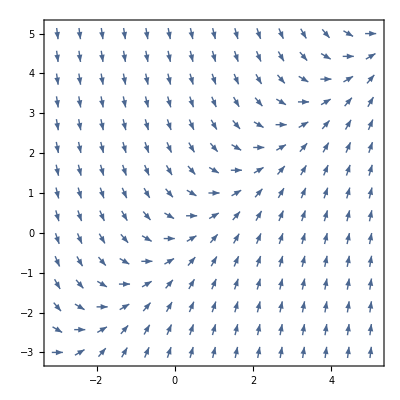

```mathematica
vec =VectorPlot[{1,x-y},{x,-3,5},{y,-3,5},VectorScale->{.025, 0.01, None}]
```

The Vector fields seems to mirror the values produced by Euler’s method in part one.

c)  Use the DSolve Command to find an analytic solution. Evaluate this at x=4 and add a text cell stating whether this supports your previous parts.

```mathematica
Clear[y];
y[x_]=y[x]/.DSolve[{y'[x]==x-y[x],y[0]==2},y[x],x];
y[4]//N
```

{3.05495}

This value is very close to the approximation made considering we only used a step size of 1 to get there.

d) Plot your solution from part c and the direction field from part b together on the same graph.

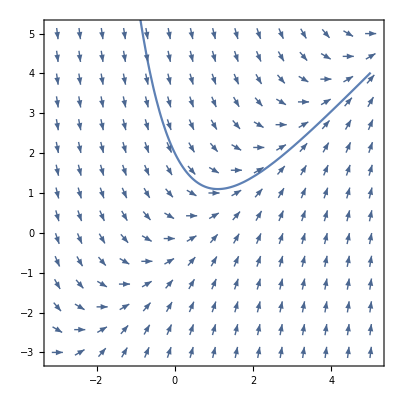

```mathematica
Show[vec,Plot[y[x],{x,-3,5}]]
```

### Problem 2

2. We would like to approximate y(4), given dy/dx=ln(x)+y+1 subject to y(1)=-2.

a)  Write either a program or a block of code that will allow you to use Euler’s Method to approximate y(4)  using n = 50 steps.

```mathematica
Subscript[x, i]=1;
Subscript[y, i]=-2;
Subscript[x, f]=4.;
n=50;
dx=(Subscript[x, f]-Subscript[x, i])/n;
f[x_,y_]:=Log[x]+y+1;
euler=Table[
Subscript[y, i]=Subscript[y, i]+f[Subscript[x, i],Subscript[y, i]] dx;
Subscript[x, i]=Subscript[x, i]+dx;
{Subscript[x, i],Subscript[y, i]},n]
```

{{1.06,-2.06},{1.12,-2.1201},{1.18,-2.18051},{1.24,-2.24141},{1.3,-2.30299},{1.36,-2.36543},{1.42,-2.4289},{1.48,-2.4936},{1.54,-2.55969},{1.6,-2.62736},{1.66,-2.69681},{1.72,-2.76821},{1.78,-2.84176},{1.84,-2.91767},{1.9,-2.99614},{1.96,-3.0774},{2.02,-3.16167},{2.08,-3.24918},{2.14,-3.34019},{2.2,-3.43495},{2.26,-3.53374},{2.32,-3.63684},{2.38,-3.74456},{2.44,-3.85721},{2.5,-3.97512},{2.56,-4.09865},{2.62,-4.22817},{2.68,-4.36407},{2.74,-4.50676},{2.8,-4.65669},{2.86,-4.81432},{2.92,-4.98013},{2.98,-5.15464},{3.04,-5.3384},{3.1,-5.53199},{3.16,-5.73603},{3.22,-5.95116},{3.28,-6.17806},{3.34,-6.41748},{3.4,-6.67017},{3.46,-6.93695},{3.52,-7.21869},{3.58,-7.5163},{3.64,-7.83076},{3.7,-8.16309},{3.76,-8.51437},{3.82,-8.88577},{3.88,-9.2785},{3.94,-9.69386},{4.,-10.1332}}

b) Generate a vector field for the DE. Use a range of 1 to 6 for x and a range of -12 to 4 for y on your plot. Add a text cell stating whether the image supports your answer from part a.

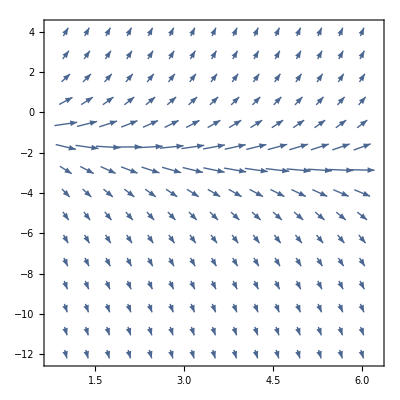

```mathematica
vec =VectorPlot[{1,Log[x]+y+1},{x,1,6},{y,-12,4},VectorScale->{.025, 0.01, None}]
```

The slope field seems to resemble the Euler approximation in step 1.

c)  Use the DSolve Command to find an analytic solution. Evaluate this at x=4 and add a text cell stating whether this supports your previous parts.

```mathematica
Clear[y];
y[x_]=y[x]/.DSolve[{y'[x]==Log[x]+y[x]+1,y[1]==-2},y[x],x];
y[4]//N
```

{-10.7002}

This value is very close to the final y value in the array from Euler’s approximation. This suggest that the approximation method is accurate and functional.

d) Plot your solution from part c and the direction field from part b together on the same graph.  Use a range of 1 to 6 for x.

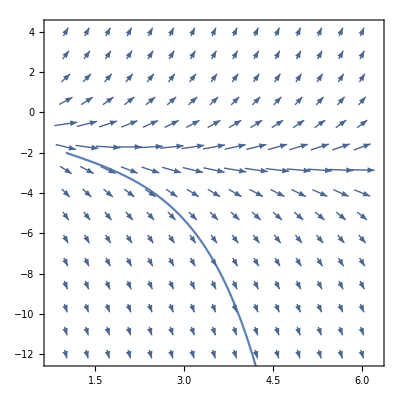

```mathematica
Show[vec,Plot[y[x],{x,1,6}]]
```